```mathematica
$Assumptions={r>0,k≥1,k∈Integers};
```

```mathematica
(* r will be the radial component of z*)
```

Implementing Friedrich’s Examples of superminimal spheres of higher degrees:

```mathematica
f=z^k;
g=(z);
```

Use Bryant’s Weierstraß Parametrisation

```mathematica
Θ={f-1/2g D[f,z]/D[g,z],g,1/2D[f,z]/D[g,z]};
```

```mathematica
n[Z_]:=Z Conjugate[Z];
nZ=1+Sum[n[Z[i]],{i,1,3}];
theta={Z[1]->Θ[[1]],Z[2]->Θ[[2]],Z[3]->Θ[[3]]};
```

#### Calculating the Kähler Potential

```mathematica
kpotential=1/2Log[nZ]/.theta//Simplify
```

1/2 Log[1/4 (4+4 z Conjugate[z]+k^2 z^(-1+k) Conjugate[z^(-1+k)]+(-2+k)^2 z^k Conjugate[z^k])]

This is radially symmetric, so we simply replace z by the positive parameter r

```mathematica
kradial=kpotential/.{z->r}//FullSimplify
```

1/2 Log[1+r^2+1/4 r^(-2+2 k) (k^2+(-2+k)^2 r^2)]

The conformally flat factor can be calculated using the Laplacian on C

```mathematica
conf=Laplacian[kradial,{r,ϕ},"Polar"]//FullSimplify
```

(32 r^4+2 (-2+k)^2 k^2 r^(4 k)+8 r^(2 k) ((-1+k)^2 k^2+2 (-2+k)^2 k^2 r^2+(2-3 k+k^2)^2 r^4))/((r^(2 k) (k^2+(-2+k)^2 r^2)+4 (r^2+r^4))^2)

Formula for the Gauß-curvature of a conformally flat metric:

```mathematica
curv=-1/(2 conf) Laplacian[Log[conf],{r,ϕ},"Polar"];
```

#### An explicit formula for α_+^2:

```mathematica
curv/.{k->2}//Simplify
```

2

Define the square of α_+

```mathematica
α2=1-curv/2//FullSimplify
```

(2 (-2+k)^2 (-1+k)^2 k^2 r^(-2+2 k) (r^(2 k) (k^2+(-2+k)^2 r^2)+4 (r^2+r^4))^4)/((16 r^4+(-2+k)^2 k^2 r^(4 k)+4 r^(2 k) ((-1+k)^2 k^2+2 (-2+k)^2 k^2 r^2+(2-3 k+k^2)^2 r^4))^3)

We see that the only zeros occur at r=0 and r=∞

```mathematica
Limit[{Sqrt[α2]r^(k-4),Sqrt[α2]r^(k-3)}/.{k->3},r->0]
```

{∞,3/(√2)}

```mathematica
Check that the PDE is satisfied:
```

```mathematica
u1=Laplacian[Log[α2],{r,ϕ},"Polar"]//Simplify
```

-((16 (-4096 r^14+3 k^10 (2-3 k+k^2)^2 r^(10 k)-96 (-2+k)^6 (-1+k)^2 k^2 (1-8 k+4 k^2) r^(6 (2+k))+3072 (-2+k)^2 (-1+k)^3 k^2 r^(4 (3+k))+3072 (-3+k) (-1+k)^3 k^2 r^(2 (5+k))+1536 (-2+k)^2 k^2 (-1-6 k+3 k^2) r^(2 (6+k))+3072 (-2+k)^2 (-1+k)^3 (1+k) r^(2 (7+k))+768 k^2 (2-3 k+k^2)^2 r^(2 (8+k))+768 k^2 (2-3 k+k^2)^2 r^(8+2 k)-768 (-1+k)^2 k^4 (-3+2 k) r^(6+4 k)-3072 (-2+k)^2 (-1+k)^3 k^2 r^(8+4 k)+768 (-2+k)^2 k^2 (9-28 k+14 k^2) r^(10+4 k)+768 (-2+k)^4 (-1+k)^2 (-1+2 k) r^(14+4 k)-64 (-1+k)^6 k^6 r^(2+6 k)-96 k^6 (2-3 k+k^2)^2 (1-8 k+4 k^2) r^(4+6 k)-192 (-2+k)^2 (-1+k)^4 k^4 (-9-10 k+5 k^2) r^(6+6 k)-64 (-2+k)^2 k^2 (-72+288 k-444 k^2+324 k^3+209 k^4-622 k^5+477 k^6-160 k^7+20 k^8) r^(8+6 k)-192 k^2 (2-3 k+k^2)^4 (-9-10 k+5 k^2) r^(10+6 k)-64 (2-3 k+k^2)^6 r^(14+6 k)+48 k^6 (-1+2 k) (2-3 k+k^2)^2 r^(2+8 k)+192 (-2+k)^2 (-1+k)^3 k^6 r^(4+8 k)+48 (-2+k)^4 k^4 (9-28 k+14 k^2) r^(6+8 k)-192 (-2+k)^6 (-1+k)^3 k^2 r^(8+8 k)-48 (-2+k)^6 (-1+k)^2 k^2 (-3+2 k) r^(10+8 k)+12 (-2+k)^4 (-1+k)^3 k^6 (1+k) r^(2+10 k)+6 (-2+k)^6 k^6 (-1-6 k+3 k^2) r^(4+10 k)+12 (-3+k) (-2+k)^6 (-1+k)^3 k^4 r^(6+10 k)+3 (-2+k)^10 (-1+k)^2 k^2 r^(8+10 k)-(-2+k)^6 k^6 r^(2+12 k)))/(r^2 (4 r^2+4 r^4+k^2 r^(2 k)+(-2+k)^2 r^(2+2 k))^2 (16 r^4+4 (-1+k)^2 k^2 r^(2 k)+(-2+k)^2 k^2 r^(4 k)+8 (-2+k)^2 k^2 r^(2+2 k)+4 (2-3 k+k^2)^2 r^(4+2 k))^2))

```mathematica
u2=-(4(3(α2)-2) conf)//Simplify
```

-(4 (64 r^4+4 (-2+k)^2 k^2 r^(4 k)+16 r^(2 k) ((-1+k)^2 k^2+2 (-2+k)^2 k^2 r^2+(2-3 k+k^2)^2 r^4)) (-2+(6 (-2+k)^2 (-1+k)^2 k^2 r^(-2+2 k) (r^(2 k) (k^2+(-2+k)^2 r^2)+4 (r^2+r^4))^4)/((16 r^4+(-2+k)^2 k^2 r^(4 k)+4 r^(2 k) ((-1+k)^2 k^2+2 (-2+k)^2 k^2 r^2+(2-3 k+k^2)^2 r^4))^3)))/((r^(2 k) (k^2+(-2+k)^2 r^2)+4 (r^2+r^4))^2)

```mathematica
u1-1/2u2 //Simplify
```

0

### Some calculations for small k:

#### k=1,2

If k=1,2 then the superminimal curve is a totally geodesic projective line

```mathematica
α2/.{{k->1},{k->2}}
```

{0,0}

#### k=3,..,7

Verifying the Gauss-Bonnet theorem

```mathematica
Table[2 π Integrate[ (r conf curv)/.{k->i},{r,0,∞}],{i,3,7}]
```

{4 π,4 π,4 π,4 π,4 π}

Friedrich computes that for k>=3 the degree d for the θ is k, which we can verify for small k since vol=d 4 π for superminimal curves

```mathematica
Table[1/2  Integrate[ (r conf)/.{k->i},{r,0,∞}],{i,3,7}]
```

{3,4,5,6,7}

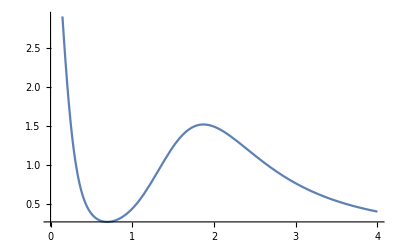
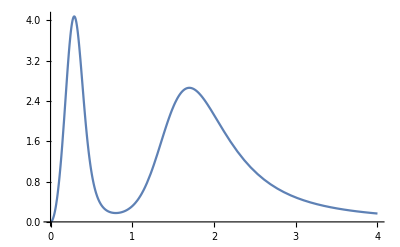
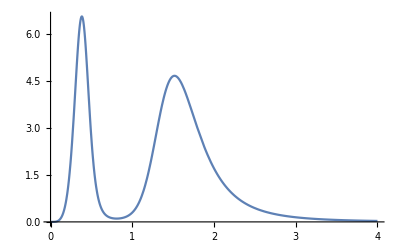
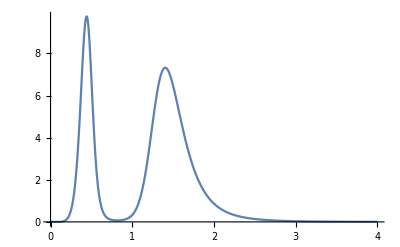

```mathematica
Table[Plot[α2/.{k->i},{r,0,4}],{i,3,6}]
```